```mathematica
ave=0;
st={};
Do[latt=Import["lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/0000.txt","Table"][[;;,1]];

ctr=0;
Do[
lprev=latt[[i-1]];
l=latt[[i]];
lnext=latt[[i+1]];
If[
l==lprev+1&&lnext==l+1,
ctr+=1;
];
,{i,2,Length[latt]-1}];

AppendTo[st,ctr];
ave+=ctr;

,{iLatt,101,200}];
ave=ave/100.0//N;
```

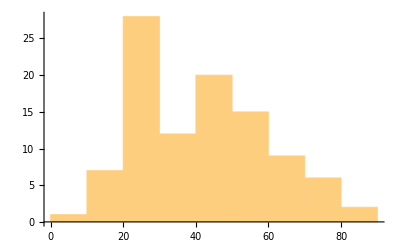

```mathematica
Histogram[st]
```

```mathematica
ave
```

40.72